```mathematica
SetDirectory[NotebookDirectory[]];
angPP = Get["COS_intang_PPtt_inc_bin_3TeV_new.txt"];
angZP = Get["Cos_intang_ZPtt_inc_bin_3TeV_new.txt"];
```

```mathematica
angWW = Get["COS_intang_WWtt_inc_bin_3TeV.txt"];
angZZ = Get["cos_intang_ZZtt_inc_bin_3TeV_new.txt"];
```

```mathematica
dytangWW = Get["DYT_COS_intang_WWtt_inc_bin.txt"];
dytangZZ = Get["DYT_intang_ZZtt_inc_bin.txt"];
```

Get::noopen: Cannot open DYT_COS_intang_WWtt_inc_bin.txt.

Get::noopen: Cannot open DYT_intang_ZZtt_inc_bin.txt.



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
lum = 1/1000;(*conv to fb from ab*)
sqrtsbin = Table[350 + 50*i, {i,0,54}];
iangZP[ang_,num_] :=angZP [[ang]][(1 + ((num - 350)/50))]
iangWW[ang_,num_] :=angWW [[ang]][(1 + ((num - 350)/50))]
iangZZ[ang_,num_] :=angZZ [[ang]][(1 + ((num - 350)/50))]
iangPP[ang_,num_] :=angPP [[ang]][(1 + ((num - 350)/50))]
```

```mathematica
thetaList=Table[0+(Pi/72)*i,{i,0,72}];
```

```mathematica
low=350;
high=3000;
```

```mathematica
intPP =Table[NIntegrate[lum*iangPP[i,en] ,{en,low,high}],{i,2,72}];
intZP =Table[NIntegrate[lum*iangZP[i,en] ,{en,low,high}],{i,2,72}];
intWW =Table[NIntegrate[lum*iangWW[i,en] ,{en,low,high}],{i,2,72}];
intZZ =Table[NIntegrate[lum*iangZZ[i,en] ,{en,low,high}],{i,2,72}];
```

```mathematica
thetaList1=Table[(Pi/72)*i,{i,1,71}];
interpp= Table[{-Cos[thetaList1[[k]]],intPP[[k]]},{k,1,71}];
interww= Table[{-Cos[thetaList1[[k]]],intWW[[k]]},{k,1,71}];
interzp= Table[{-Cos[thetaList1[[k]]],intZP[[k]]},{k,1,71}];
interzz= Table[{-Cos[thetaList1[[k]]],intZZ[[k]]},{k,1,71}];
sumall = Table[{-Cos[thetaList1[[k]]],intPP[[k]]+intWW[[k]]+intZZ[[k]]+intZP[[k]]},{k,1,71}];
```

```mathematica
pp= Interpolation[interpp]
ww= Interpolation[interww]
zp= Interpolation[interzp]
zz= Interpolation[interzz]
sum =  Interpolation[sumall]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«2 more identical outputs»

```mathematica
SetDirectory[NotebookDirectory[]];
<<CustomTicks`
ticks0=LogTicks[10,-2,4,TickLabelStep->1];
ticks1=ticks0;
Do[ticks1[[i,1]]=10^(ticks0[[i,1]]),{i,1,Length[ticks0]}]
ticks1[[7,1]]
```

10000.

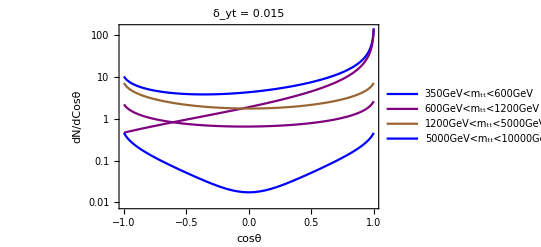

```mathematica
ListLogPlot[{sum,ww,pp,zz,zp},Joined->True,Frame->True,PlotStyle->{Blue,Purple,Brown},
PlotLabel->Style["δ_yt = 0.015 ",Black,20],
PlotLegends->{"350GeV<m_tt<600GeV","600GeV<m_tt<1200GeV","1200GeV<m_tt<5000GeV","5000GeV<m_tt<10000GeV"},FrameLabel->{Style["cosθ",Black,20],Style["dN/dCosθ",Black,15]},FrameTicksStyle->Directive[Black,13]]
```

```mathematica
N[Table[Cos[thetaList1[[k]]],{k,1,70}]]
```

{0.999048,0.996195,0.991445,0.984808,0.976296,0.965926,0.953717,0.939693,0.92388,0.906308,0.887011,0.866025,0.843391,0.819152,0.793353,0.766044,0.737277,0.707107,0.67559,0.642788,0.608761,0.573576,0.5373,0.5,0.461749,0.422618,0.382683,0.34202,0.300706,0.258819,0.21644,0.173648,0.130526,0.0871557,0.0436194,0.,-0.0436194,-0.0871557,-0.130526,-0.173648,-0.21644,-0.258819,-0.300706,-0.34202,-0.382683,-0.422618,-0.461749,-0.5,-0.5373,-0.573576,-0.608761,-0.642788,-0.67559,-0.707107,-0.737277,-0.766044,-0.793353,-0.819152,-0.843391,-0.866025,-0.887011,-0.906308,-0.92388,-0.939693,-0.953717,-0.965926,-0.976296,-0.984808,-0.991445,-0.996195}

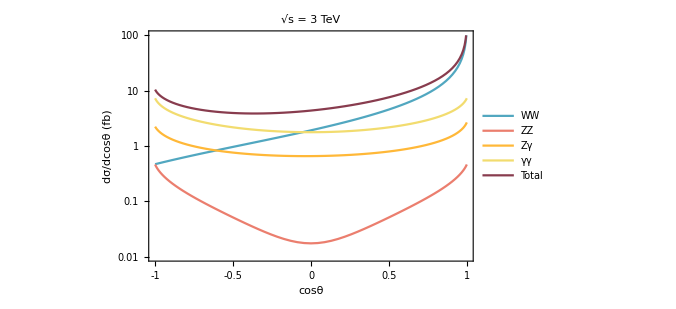

```mathematica
lineplot=ListLogPlot[{ww,zz,zp,pp,sum},Joined->True,PlotStyle->{ColorData[colorselecitonumber][5],ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][9]},Frame->True,FrameLabel->{Style[DisplayForm["cosθ"],Black,17,FontFamily->"Times"],Style["dσ/dcosθ (fb)",Black,17,FontFamily->"Times"]},
PlotLabel->Style[DisplayForm[SqrtBox["s"] ]  Row[{" = ",3 TeV}]  ,Black,17,FontFamily->"Times"],
(*PlotLegends->{Style[" Total ",Black,22,FontFamily->"Times"],Style[" WW ",Black,22,FontFamily->"Times"],Style[" ZZ ",Black,22,FontFamily->"Times"],Style[" Zγ ",Black,22,FontFamily->"Times"],Style[" γγ ",Black,22,FontFamily->"Times"]},*)
PlotLegends->{Placed[LineLegend[{Style[" WW ",Black,15,FontFamily->"Times"],Style[" ZZ ",Black,15,FontFamily->"Times"],Style[" Zγ ",Black,15,FontFamily->"Times"],Style[" γγ ",Black,15,FontFamily->"Times"],Style[" Total ",Black,15,FontFamily->"Times"]},LegendLayout->{"Row",3}],{{0.22,0.76},{0.25,0.3}}]},
PlotRange->{{-1,1},{0.01,100}},FrameTicks->{{ticks1,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
```

```mathematica
Export["angular_dist_3TeV.pdf",lineplot]
```

angular_dist_3TeV.pdf